```mathematica
(*Исходные данные:*)
Subscript[V, 0]=52 ;
Subscript[θ, c0]=39 ;
ṁ=79 ;
Subscript[y, 0]=2150;
Subscript[ω, z0]=0;
Subscript[ϑ, 0]=Subscript[θ, c0];
Subscript[t, 0]=Subscript[x, 0]=0;
tk=4.73;
Subscript[m, 0]=1160;
Subscript[J, z]=120;
Subscript[l, dc]=0.22;
Subscript[S, a]=0.15;
Subscript[S, m]=0.2289;
Subscript[ρ, oN]=1.225;
Subscript[p, oN]=101325;
Subscript[T, oN]=288.15;
Subscript[g, oN]=9.80665;
r=6356767;
tab1={{0.01,0.30},{0.55,0.30},{0.8,0.55},{0.9,0.70},{1.0,0.84},
{1.06,0.86},{1.1,0.87},{1.2,0.83},{1.3,0.80},{1.4,0.79},
{2.0,0.65},{2.6,0.55},{3.4,0.50},{6.0,0.45},{10.0,0.40}} ;
(*tab1 - таблица аэродинамических коэффициентов Cxa(M)*)
tab2={{0.01,0.25},{0.55,0.25},{0.8,0.25},{0.9,0.20},{1.0,0.30},
{1.06,0.31},{1.1,0.25},{1.2,0.25},{1.3,0.25},{1.4,0.25},
{2.0,0.25},{2.6,0.25},{3.4,0.25},{6.0,0.25},{10.0,0.25}} ;
(*tab2 - таблица аэродинамических коэффициентов Cya(M)*)
(*Таблицы обязательно должны быть записаны по возрастанию числа Маха*)

(*Этап 1. Линейная интерполяция аэродинамических коэффициентов*)
n1=Count[{tab1}, _Real, Infinity]/2 (*Количество точек, заданных таблицей 1 аэродинамических коэффициентов Cxa(M)*);
n2=Count[{tab2}, _Real, Infinity]/2 (*Количество точек, заданных таблицей 2 аэродинамических коэффициентов Cxy(M)*);
```

```mathematica
arg1[M_]:=Catch[Do[If  [(M>=tab1[[i,1]])&& (M<tab1[[i+1,1]]),Throw[i]],{i,1,n1-1}]](*номер промежутка, в который попадает число Маха, он же номер точки начала промежутка, т.е. в моей программе n-ый промежуток находится между точкой n и n+1*)
Cxa[M_]:=If[( M>=tab1[[1,1]])&& (M<tab1[[n1,1]]), (tab1[[arg1[M]+1,2]]-tab1[[arg1[M],2]])/(tab1[[arg1[M]+1,1]]-tab1[[arg1[M],1]])*(M-tab1[[arg1[M],1]])+tab1[[arg1[M],2]], If[M>=tab1[[n1,1]], (tab1[[n1,2]]-tab1[[n1-1,2]])/(tab1[[n1,1]]-tab1[[n1-1,1]])*(M-tab1[[n1,1]])+tab1[[n1,2]],(tab1[[2,2]]-tab1[[1,2]])/(tab1[[2,1]]-tab1[[1,1]])*(M-tab1[[1,1]])+tab1[[1,2]]]]
```

```mathematica
arg2[M_]:=Catch[Do[If  [(M>=tab2[[i,1]])&& (M<tab2[[i+1,1]]),Throw[i]],{i,1,n2-1}]]
Cya[M_]:=If[( M>=tab2[[1,1]])&& (M<tab2[[n2,1]]), (tab2[[arg2[M]+1,2]]-tab2[[arg2[M],2]])/(tab2[[arg2[M]+1,1]]-tab2[[arg2[M],1]])*(M-tab2[[arg2[M],1]])+tab2[[arg2[M],2]], If[M>=tab2[[n2,1]], (tab2[[n2,2]]-tab2[[n2-1,2]])/(tab2[[n2,1]]-tab2[[n2-1,1]])*(M-tab2[[n2,1]])+tab2[[n2,2]],(tab2[[2,2]]-tab2[[1,2]])/(tab2[[2,1]]-tab2[[1,1]])*(M-tab2[[1,1]])+tab2[[1,2]]]]
```

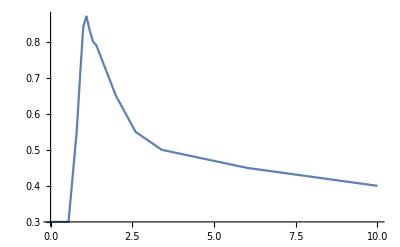

```mathematica
Plot[Cxa[M], {M,0,10}]
```

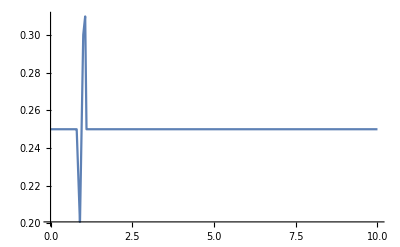

```mathematica
Plot[Cya[M], {M,0,10}]
```

```mathematica
(*Этап 2. Задание математической модели*)
```

```mathematica
m[t_]:= If[t>tk, Subscript[m, 0]-ṁ*tk,Subscript[m, 0]-ṁ*t];
Subscript[P, 0]=2100 ṁ;
ℼ[y_]:=(1-2.26*10^-5 y)^5.2559;
H[y_]:=(1-2.26*10^-5 y)^4.2559;
a[y_]:=20.0468 √(Subscript[T, oN]-0.0065y);
g[y_]:=Subscript[g, oN](r/(r+y))^2;
P[y_,t_]:=If[t>tk,0,Subscript[P, 0]+Subscript[S, a]*Subscript[p, oN](1-ℼ[y])];
M[V_,y_]:=V/a[y];
Subscript[X, a][V_,y_]:=Cxa[M[V,y]] Subscript[S, m](Subscript[ρ, oN] H[y])/2 V^2;
Subscript[Y, a][V_,y_,α_]:=Cya[M[V,y]] Subscript[S, m] α(Subscript[ρ, oN] H[y])/2 V^2;
Subscript[M, z][V_,y_,α_]:=-(Cxa[M[V,y]]+Cya[M[V,y]]α)Subscript[S, m](Subscript[ρ, oN] H[y])/2 V^2 Subscript[l, dc];
Subscript[α, 0]=Subscript[ϑ, 0]-Subscript[θ, c0];
```

```mathematica
(*Этап 3. Интегрирование численным методом Эйлера*)
Eiler[Δt_]:=(
RezTab={{"N","t,c","m,кг","Р,Н","V,м/c","M","C_xa","α,град","θ_c,град","C_ya","dV/dt,м/(:0441)^2","ω_z,1/с",
"ϑ,град","y,м","dy/dt,м/c","x,м","dx/dt,м/c"},{0,1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16},
{1,Subscript[t, 0],m[Subscript[t, 0]],P[Subscript[y, 0],Subscript[t, 0]],Subscript[V, 0],M[Subscript[V, 0],Subscript[y, 0]],Cxa[M[Subscript[V, 0],Subscript[y, 0]]],Subscript[α, 0],Subscript[θ, c0],Cya[M[Subscript[V, 0],Subscript[y, 0]]],
(P[Subscript[y, 0],Subscript[t, 0]]*Cos[Subscript[α, 0]*Pi/180]-Subscript[X, a][Subscript[V, 0],Subscript[y, 0]])/m[Subscript[t, 0]]-g[Subscript[y, 0]]*Sin[Subscript[θ, c0]*Pi/180],Subscript[ω, z0],Subscript[ϑ, 0],Subscript[y, 0],Subscript[V, 0] Sin[Subscript[θ, c0]*Pi/180],Subscript[x, 0],Subscript[V, 0] Cos[Subscript[θ, c0]*Pi/180]}};
tkpass=False;
Δt1=Δt;
n=1;
Subscript[x, с]=Subscript[x, 0];
Subscript[y, с]=Subscript[y, 0];
Subscript[t, с]=Subscript[t, 0];
Subscript[ϑ, с]=Subscript[ϑ, 0]*Pi/180;
Subscript[θ, cс]=Subscript[θ, c0]*Pi/180;
Subscript[ω, zс]=Subscript[ω, z0];
Subscript[V, с]=Subscript[V, 0];
While[Subscript[y, с]>0,
Subscript[t, н]=Subscript[t, с]+Δt1;
Subscript[α, с]=Subscript[ϑ, с]-Subscript[θ, cс];
Subscript[x, н]=Subscript[x, с]+Subscript[V, с] Cos[Subscript[θ, cс]]Δt1;
Subscript[y, н]=Subscript[y, с]+Subscript[V, с] Sin[Subscript[θ, cс]]Δt1;
Subscript[ϑ, н]=Subscript[ϑ, с]+Subscript[ω, zс] Δt1;
Subscript[V, н]=Subscript[V, с]+((P[Subscript[y, с],Subscript[t, с]]Cos[Subscript[α, с]]-Subscript[X, a][Subscript[V, с],Subscript[y, с]])/m[Subscript[t, с]]-g[Subscript[y, с]]Sin[Subscript[θ, cс]])Δt1;
Subscript[ω, zн]=Subscript[ω, zс]+(Subscript[M, z][Subscript[V, с],Subscript[y, с],Subscript[α, с]])/Subscript[J, z] Subscript[α, с] Δt1;
Subscript[θ, cн]=Subscript[θ, cс]+((P[Subscript[y, с],Subscript[t, с]]Sin[Subscript[α, с]]-Subscript[Y, a][Subscript[V, с],Subscript[y, с],Subscript[α, с]])/(m[Subscript[t, с]]*Subscript[V, с])-(g[Subscript[y, с]]Cos[Subscript[θ, cс]])/Subscript[V, с])Δt1;
Subscript[α, н]=Subscript[ϑ, н]-Subscript[θ, cн];
Subscript[t, с]=Subscript[t, н];
Subscript[x, с]=Subscript[x, н];
Subscript[y, с]=Subscript[y, н];
Subscript[ϑ, с]=Subscript[ϑ, н];
Subscript[V, с]=Subscript[V, н];
Subscript[ω, zс]=Subscript[ω, zн];
Subscript[θ, cс]=Subscript[θ, cн];

If[(Subscript[t, н]<5  && (Mod[Subscript[t, н]*10,1]<0.00001||Mod[Subscript[t, н]*10,1]>0.9999))||Abs[tk-Subscript[t, н]]<0.00001||(Subscript[t, н]>=5  && (Mod[Subscript[t, н],1]<0.00001||Mod[Subscript[t, н],1]>0.9999)),
n++;
AppendTo[RezTab,{n,Subscript[t, н],m[Subscript[t, н]],P[Subscript[y, н],Subscript[t, н]],Subscript[V, н],M[Subscript[V, н],Subscript[y, н]],Cxa[M[Subscript[V, н],Subscript[y, н]]],Subscript[α, н]*180/Pi,Subscript[θ, cн]*180/Pi,Cya[M[Subscript[V, н],Subscript[y, н]]],(P[Subscript[y, н],Subscript[t, н]]*Cos[Subscript[α, н]]-Subscript[X, a][Subscript[V, н],Subscript[y, н]])/m[Subscript[t, н]]-g[Subscript[y, н]]*Sin[Subscript[θ, cн]],Subscript[ω, zн],Subscript[ϑ, н]*180/Pi,Subscript[y, н],Subscript[V, н] Sin[Subscript[θ, cн]],Subscript[x, н],Subscript[V, н] Cos[Subscript[θ, cн]]}]];
If[Abs[tk-Subscript[t, н]]<0.00001,tkpass=True];(*ловим tk*)

If[Not[tkpass]&&tk-Subscript[t, н]<(Δt-0.0001),
Δt2=tk-Subscript[t, н];
Subscript[t, н]=Subscript[t, с]+Δt2;
Subscript[α, с]=Subscript[ϑ, с]-Subscript[θ, cс];
Subscript[x, н]=Subscript[x, с]+Subscript[V, с]*Cos[Subscript[θ, cс]]*Δt2;
Subscript[y, н]=Subscript[y, с]+Subscript[V, с]*Sin[Subscript[θ, cс]]*Δt2;
Subscript[ϑ, н]=Subscript[ϑ, с]+Subscript[ω, zс] Δt2;
Subscript[V, н]=Subscript[V, с]+((P[Subscript[y, с],Subscript[t, с]]*Cos[Subscript[α, с]]-Subscript[X, a][Subscript[V, с],Subscript[y, с]])/m[Subscript[t, с]]-g[Subscript[y, с]]*Sin[Subscript[θ, cс]])*Δt2;
Subscript[ω, zн]=Subscript[ω, zс]+(Subscript[M, z][Subscript[V, с],Subscript[y, с],Subscript[α, с]])/Subscript[J, z] Subscript[α, с] Δt2;
Subscript[θ, cн]=Subscript[θ, cс]+((P[Subscript[y, с],Subscript[t, с]]*Sin[Subscript[α, с]]-Subscript[Y, a][Subscript[V, с],Subscript[y, с],Subscript[α, с]])/(m[Subscript[t, с]]*Subscript[V, с])-(g[Subscript[y, с]]*Cos[Subscript[θ, cс]])/Subscript[V, с])*Δt2;
Subscript[α, н]=Subscript[ϑ, н]-Subscript[θ, cн];
Subscript[t, с]=Subscript[t, н];
Subscript[x, с]=Subscript[x, н];
Subscript[y, с]=Subscript[y, н];
Subscript[ϑ, с]=Subscript[ϑ, н];
Subscript[V, с]=Subscript[V, н];
Subscript[ω, zс]=Subscript[ω, zн];
Subscript[θ, cс]=Subscript[θ, cн];

n++;
AppendTo[RezTab,{n,Subscript[t, н],m[Subscript[t, н]],P[Subscript[y, н],Subscript[t, н]],Subscript[V, н],M[Subscript[V, н],Subscript[y, н]],Cxa[M[Subscript[V, н],Subscript[y, н]]],Subscript[α, н]*180/Pi,Subscript[θ, cн]*180/Pi,Cya[M[Subscript[V, н],Subscript[y, н]]],(P[Subscript[y, н],Subscript[t, н]]*Cos[Subscript[α, н]]-Subscript[X, a][Subscript[V, н],Subscript[y, н]])/m[Subscript[t, н]]-g[Subscript[y, н]]*Sin[Subscript[θ, cн]],Subscript[ω, zн],Subscript[ϑ, н]*180/Pi,Subscript[y, н],Subscript[V, н] Sin[Subscript[θ, cн]],Subscript[x, н],Subscript[V, н] Cos[Subscript[θ, cн]]}];
Δt3=Δt-Δt2;
Subscript[t, н]=Subscript[t, с]+Δt3;
Subscript[α, с]=Subscript[ϑ, с]-Subscript[θ, cс];
Subscript[x, н]=Subscript[x, с]+Subscript[V, с]*Cos[Subscript[θ, cс]]*Δt3;
Subscript[y, н]=Subscript[y, с]+Subscript[V, с]*Sin[Subscript[θ, cс]]*Δt3;
Subscript[ϑ, н]=Subscript[ϑ, с]+Subscript[ω, zс] Δt3;
Subscript[V, н]=Subscript[V, с]+((P[Subscript[y, с],Subscript[t, с]]*Cos[Subscript[α, с]]-Subscript[X, a][Subscript[V, с],Subscript[y, с]])/m[Subscript[t, с]]-g[Subscript[y, с]]*Sin[Subscript[θ, cс]])*Δt3;
Subscript[ω, zн]=Subscript[ω, zс]+(Subscript[M, z][Subscript[V, с],Subscript[y, с],Subscript[α, с]])/Subscript[J, z] Subscript[α, с] Δt3;
Subscript[θ, cн]=Subscript[θ, cс]+((P[Subscript[y, с],Subscript[t, с]]*Sin[Subscript[α, с]]-Subscript[Y, a][Subscript[V, с],Subscript[y, с],Subscript[α, с]])/(m[Subscript[t, с]]*Subscript[V, с])-(g[Subscript[y, с]]*Cos[Subscript[θ, cс]])/Subscript[V, с])*Δt3;
Subscript[α, н]=Subscript[ϑ, н]-Subscript[θ, cн];
Subscript[t, с]=Subscript[t, н];
Subscript[x, с]=Subscript[x, н];
Subscript[y, с]=Subscript[y, н];
Subscript[ϑ, с]=Subscript[ϑ, н];
Subscript[V, с]=Subscript[V, н];
Subscript[ω, zс]=Subscript[ω, zн];
Subscript[θ, cс]=Subscript[θ, cн];

n++;
AppendTo[RezTab,{n,Subscript[t, н],m[Subscript[t, н]],P[Subscript[y, н],Subscript[t, н]],Subscript[V, н],M[Subscript[V, н],Subscript[y, н]],Cxa[M[Subscript[V, н],Subscript[y, н]]],Subscript[α, н]*180/Pi,Subscript[θ, cн]*180/Pi,Cya[M[Subscript[V, н],Subscript[y, н]]],(P[Subscript[y, н],Subscript[t, н]]*Cos[Subscript[α, н]]-Subscript[X, a][Subscript[V, н],Subscript[y, н]])/m[Subscript[t, н]]-g[Subscript[y, н]]*Sin[Subscript[θ, cн]],Subscript[ω, zн],Subscript[ϑ, н]*180/Pi,Subscript[y, н],Subscript[V, н] Sin[Subscript[θ, cн]],Subscript[x, н],Subscript[V, н] Cos[Subscript[θ, cн]]}];
tkpass=True;
];

];
n++;
AppendTo[RezTab,{n,Subscript[t, н],m[Subscript[t, н]],P[Subscript[y, н],Subscript[t, н]],Subscript[V, н],M[Subscript[V, н],Subscript[y, н]],Cxa[M[Subscript[V, н],Subscript[y, н]]],Subscript[α, н]*180/Pi,Subscript[θ, cн]*180/Pi,Cya[M[Subscript[V, н],Subscript[y, н]]],(P[Subscript[y, н],Subscript[t, н]]*Cos[Subscript[α, н]]-Subscript[X, a][Subscript[V, н],Subscript[y, н]])/m[Subscript[t, н]]-g[Subscript[y, н]]*Sin[Subscript[θ, cн]],Subscript[ω, zн],Subscript[ϑ, н]*180/Pi,Subscript[y, н],Subscript[V, н] Sin[Subscript[θ, cн]],Subscript[x, н],Subscript[V, н] Cos[Subscript[θ, cн]]}];
);
Clear[RezTab]
Eiler[0.001]
Grid[RezTab,Frame->All]
```

N | t,c | m,кг | Р,Н | V,м/c | M | C_xa | α,град | θ_c,град | C_ya | dV/dt,м/с^2 | ω_z,1/с | ϑ,град | y,м | dy/dt,м/c | x,м | dx/dt,м/c
0 | 1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12 | 13 | 14 | 15 | 16
1 | 0 | 1160 | 169401. | 52 | 0.156655 | 0.3 | 0 | 39 | 0.25 | 139.788 | 0 | 39 | 2150 | 52 Sin[(13 π)/60] | 0 | 52 Cos[(13 π)/60]
2 | 0.1 | 1152.1 | 169406. | 66.0305 | 0.198932 | 0.3 | 0.66202 | 38.3377 | 0.25 | 140.824 | -0.000145419 | 38.9997 | 2153.68 | 40.9585 | 4.60389 | 51.7923
3 | 0.2 | 1144.2 | 169413. | 80.1626 | 0.241521 | 0.3 | 1.08847 | 37.9091 | 0.25 | 141.823 | -0.000676704 | 38.9976 | 2158.19 | 49.2528 | 10.3495 | 63.2472
4 | 0.3 | 1136.3 | 169421. | 94.3937 | 0.284416 | 0.3 | 1.38099 | 37.61 | 0.25 | 142.808 | -0.00173146 | 38.991 | 2163.52 | 57.607 | 17.2443 | 74.7771
5 | 0.4 | 1128.4 | 169430. | 108.723 | 0.327615 | 0.3 | 1.58714 | 37.3895 | 0.25 | 143.786 | -0.00344271 | 38.9766 | 2169.7 | 66.0198 | 25.2959 | 86.3833
6 | 0.5 | 1120.5 | 169440. | 123.15 | 0.371119 | 0.3 | 1.73093 | 37.2193 | 0.25 | 144.762 | -0.00593353 | 38.9502 | 2176.72 | 74.4893 | 34.5119 | 98.0675
7 | 0.6 | 1112.6 | 169451. | 137.674 | 0.414928 | 0.3 | 1.82466 | 37.0824 | 0.25 | 145.738 | -0.00930933 | 38.9071 | 2184.59 | 83.0126 | 44.9004 | 109.832
8 | 0.7 | 1104.7 | 169464. | 152.297 | 0.459044 | 0.3 | 1.87429 | 36.9676 | 0.25 | 146.716 | -0.0136476 | 38.8419 | 2193.32 | 91.5856 | 56.4694 | 121.681
9 | 0.8 | 1096.8 | 169478. | 167.017 | 0.50347 | 0.3 | 1.88211 | 36.8669 | 0.25 | 147.697 | -0.0189851 | 38.7491 | 2202.9 | 100.203 | 69.2277 | 133.619
10 | 0.9 | 1088.9 | 169493. | 181.835 | 0.548208 | 0.3 | 1.84836 | 36.7745 | 0.25 | 148.681 | -0.0253028 | 38.6228 | 2213.35 | 108.859 | 83.1842 | 145.65
11 | 1. | 1081. | 169509. | 196.744 | 0.593236 | 0.343236 | 1.77145 | 36.6855 | 0.25 | 149.495 | -0.0329995 | 38.4569 | 2224.67 | 117.539 | 98.3486 | 157.774
12 | 1.1 | 1073.1 | 169527. | 211.731 | 0.638519 | 0.388519 | 1.64555 | 36.596 | 0.25 | 150.247 | -0.042594 | 38.2415 | 2236.85 | 126.228 | 114.73 | 169.991
13 | 1.2 | 1065.2 | 169546. | 226.791 | 0.684039 | 0.434039 | 1.46405 | 36.5022 | 0.25 | 150.934 | -0.0538472 | 37.9662 | 2249.9 | 134.907 | 132.338 | 182.302
14 | 1.3 | 1057.3 | 169566. | 241.915 | 0.729778 | 0.479778 | 1.22252 | 36.4006 | 0.25 | 151.547 | -0.066123 | 37.6232 | 2263.82 | 143.559 | 151.181 | 194.714
15 | 1.4 | 1049.4 | 169587. | 257.097 | 0.775712 | 0.525712 | 0.921177 | 36.2882 | 0.25 | 152.076 | -0.0782745 | 37.2094 | 2278.6 | 152.162 | 171.272 | 207.233
16 | 1.5 | 1041.5 | 169610. | 272.325 | 0.821811 | 0.582716 | 0.567708 | 36.1626 | 0.239095 | 152.423 | -0.0886202 | 36.7303 | 2294.24 | 160.693 | 192.619 | 219.86
17 | 1.6 | 1033.6 | 169634. | 287.574 | 0.867999 | 0.651999 | 0.179468 | 36.0223 | 0.216 | 152.534 | -0.0950405 | 36.2018 | 2310.73 | 169.122 | 215.234 | 232.586
18 | 1.7 | 1025.7 | 169658. | 302.826 | 0.914225 | 0.719915 | -0.212886 | 35.8675 | 0.214225 | 152.495 | -0.0945579 | 35.6546 | 2328.05 | 177.43 | 239.127 | 245.403
19 | 1.8 | 1017.8 | 169684. | 318.068 | 0.960448 | 0.784627 | -0.563444 | 35.7001 | 0.260448 | 152.319 | -0.0843198 | 35.1366 | 2346.2 | 185.606 | 264.305 | 258.298
20 | 1.9 | 1009.9 | 169712. | 333.285 | 1.00662 | 0.842208 | -0.815515 | 35.5247 | 0.301104 | 152.057 | -0.0627935 | 34.7092 | 2365.16 | 193.657 | 290.775 | 271.249
21 | 2. | 1002. | 169740. | 348.498 | 1.05282 | 0.857607 | -0.914809 | 35.348 | 0.308803 | 152.198 | -0.0321404 | 34.4332 | 2384.92 | 201.62 | 318.543 | 284.254
22 | 2.1 | 994.1 | 169769. | 363.724 | 1.09909 | 0.869772 | -0.831571 | 35.1777 | 0.251368 | 152.321 | 0.00213423 | 34.3461 | 2405.48 | 209.547 | 347.614 | 297.297
23 | 2.2 | 986.2 | 169799. | 378.983 | 1.14549 | 0.851805 | -0.574089 | 35.0215 | 0.25 | 152.863 | 0.0320384 | 34.4475 | 2426.83 | 217.492 | 377.99 | 310.363
24 | 2.3 | 978.3 | 169831. | 394.297 | 1.19209 | 0.833164 | -0.197403 | 34.8852 | 0.25 | 153.424 | 0.0494177 | 34.6878 | 2448.97 | 225.512 | 409.674 | 323.441
25 | 2.4 | 970.4 | 169863. | 409.664 | 1.23889 | 0.818333 | 0.208403 | 34.7707 | 0.25 | 153.919 | 0.0490723 | 34.9791 | 2471.92 | 233.629 | 442.665 | 336.515
26 | 2.5 | 962.5 | 169897. | 425.08 | 1.28587 | 0.804238 | 0.538829 | 34.6757 | 0.25 | 154.4 | 0.0299975 | 35.2146 | 2495.69 | 241.841 | 476.963 | 349.579
27 | 2.6 | 954.6 | 169932. | 440.539 | 1.33303 | 0.796697 | 0.70226 | 34.5943 | 0.25 | 154.744 | -0.00351734 | 35.2965 | 2520.29 | 250.121 | 512.568 | 362.649
28 | 2.7 | 946.7 | 169967. | 456.027 | 1.38032 | 0.791968 | 0.648119 | 34.5179 | 0.25 | 155.018 | -0.0423185 | 35.166 | 2545.71 | 258.414 | 549.481 | 375.743
29 | 2.8 | 938.8 | 170004. | 471.545 | 1.42773 | 0.783529 | 0.389233 | 34.4382 | 0.25 | 155.376 | -0.0739051 | 34.8274 | 2571.96 | 266.666 | 587.706 | 388.9
30 | 2.9 | 930.9 | 170042. | 487.103 | 1.47532 | 0.772425 | 0.00784525 | 34.349 | 0.25 | 155.802 | -0.0865899 | 34.3569 | 2599.03 | 274.84 | 627.251 | 402.16
31 | 3. | 923. | 170081. | 502.705 | 1.52308 | 0.761281 | -0.365852 | 34.2488 | 0.25 | 156.23 | -0.0745702 | 33.8829 | 2626.92 | 282.916 | 668.128 | 415.536
32 | 3.1 | 915.1 | 170121. | 518.349 | 1.57102 | 0.750095 | -0.597396 | 34.1406 | 0.25 | 156.667 | -0.0408212 | 33.5432 | 2655.6 | 290.91 | 710.349 | 429.019
33 | 3.2 | 907.2 | 170161. | 534.038 | 1.61914 | 0.738866 | -0.598789 | 34.0312 | 0.25 | 157.125 | 0.00291962 | 33.4324 | 2685.09 | 298.871 | 753.921 | 442.575
34 | 3.3 | 899.3 | 170203. | 549.774 | 1.66746 | 0.727592 | -0.367526 | 33.9286 | 0.25 | 157.604 | 0.0397765 | 33.5611 | 2715.37 | 306.862 | 798.851 | 456.166
35 | 3.4 | 891.4 | 170246. | 565.559 | 1.71598 | 0.716272 | 0.00444455 | 33.8389 | 0.25 | 158.098 | 0.054192 | 33.8433 | 2746.46 | 314.937 | 845.141 | 469.757
36 | 3.5 | 883.5 | 170290. | 581.394 | 1.7647 | 0.704904 | 0.361192 | 33.7635 | 0.25 | 158.604 | 0.0389948 | 34.1247 | 2778.35 | 323.119 | 892.789 | 483.335
37 | 3.6 | 875.6 | 170335. | 597.28 | 1.81363 | 0.693486 | 0.546286 | 33.6989 | 0.25 | 159.131 | -0.000131365 | 34.2452 | 2811.07 | 331.388 | 941.794 | 496.916
38 | 3.7 | 867.7 | 170380. | 613.221 | 1.86279 | 0.682016 | 0.474977 | 33.6379 | 0.25 | 159.693 | -0.045734 | 34.1129 | 2844.62 | 339.689 | 992.16 | 510.54
39 | 3.8 | 859.8 | 170427. | 629.219 | 1.91218 | 0.670491 | 0.180182 | 33.5729 | 0.25 | 160.289 | -0.0759503 | 33.7531 | 2879. | 347.957 | 1043.89 | 524.255
40 | 3.9 | 851.9 | 170475. | 645.279 | 1.96182 | 0.658909 | -0.195789 | 33.4993 | 0.25 | 160.915 | -0.0752425 | 33.3035 | 2914.2 | 356.147 | 1097. | 538.093
41 | 4. | 844. | 170523. | 661.402 | 2.01171 | 0.648048 | -0.466339 | 33.4177 | 0.25 | 161.531 | -0.0429717 | 32.9513 | 2950.22 | 364.259 | 1151.5 | 552.058
42 | 4.1 | 836.1 | 170573. | 677.58 | 2.06184 | 0.639694 | -0.493403 | 33.3334 | 0.25 | 162.042 | 0.00531021 | 32.84 | 2987.05 | 372.337 | 1207.4 | 566.109
43 | 4.2 | 828.2 | 170623. | 693.811 | 2.11219 | 0.631302 | -0.261699 | 33.254 | 0.25 | 162.583 | 0.0445829 | 32.9923 | 3024.68 | 380.452 | 1264.71 | 580.198
44 | 4.3 | 820.3 | 170674. | 710.097 | 2.16277 | 0.622871 | 0.104813 | 33.1848 | 0.25 | 163.144 | 0.0530207 | 33.2896 | 3063.13 | 388.665 | 1323.43 | 594.287
45 | 4.4 | 812.4 | 170726. | 726.44 | 2.2136 | 0.614399 | 0.402535 | 33.1265 | 0.25 | 163.727 | 0.0248345 | 33.529 | 3102.41 | 396.991 | 1383.55 | 608.369
46 | 4.5 | 804.5 | 170779. | 742.843 | 2.26469 | 0.605885 | 0.460389 | 33.0745 | 0.25 | 164.343 | -0.0245846 | 33.5349 | 3142.53 | 405.391 | 1445.09 | 622.474
47 | 4.6 | 796.6 | 170833. | 759.309 | 2.31604 | 0.597326 | 0.243784 | 33.0215 | 0.25 | 165.001 | -0.0660439 | 33.2653 | 3183.48 | 413.789 | 1508.04 | 636.655
48 | 4.7 | 788.7 | 170888. | 775.843 | 2.36768 | 0.588721 | -0.116679 | 32.9619 | 0.25 | 165.693 | -0.0737713 | 32.8453 | 3225.27 | 422.122 | 1572.41 | 650.958
49 | 4.73 | 786.33 | 170905. | 780.817 | 2.38322 | 0.586129 | -0.219752 | 32.9425 | 0.25 | 165.908 | -0.0679725 | 32.7228 | 3237.97 | 424.606 | 1592. | 655.275
50 | 4.8 | 786.33 | 0 | 777.448 | 2.3738 | 0.587701 | -0.404575 | 32.9007 | 0.25 | -51.0142 | -0.0422182 | 32.4961 | 3267.62 | 422.298 | 1637.79 | 652.756
51 | 4.9 | 786.33 | 0 | 772.377 | 2.35952 | 0.59008 | -0.443829 | 32.841 | 0.25 | -50.3966 | 0.00884729 | 32.3971 | 3309.68 | 418.867 | 1702.87 | 648.935
52 | 5. | 786.33 | 0 | 767.368 | 2.34541 | 0.592431 | -0.209255 | 32.7805 | 0.25 | -49.7888 | 0.0478389 | 32.5713 | 3351.4 | 415.47 | 1767.58 | 645.165
53 | 6. | 786.33 | 0 | 720.435 | 2.21277 | 0.614539 | 0.426575 | 32.1429 | 0.25 | -44.2216 | 0.024204 | 32.5695 | 3750.51 | 383.295 | 2394.83 | 610.009
54 | 7. | 786.33 | 0 | 678.645 | 2.09394 | 0.634343 | 0.495307 | 31.4591 | 0.25 | -39.4793 | -0.0390518 | 31.9544 | 4119.02 | 354.178 | 2988.98 | 578.893
55 | 8. | 786.33 | 0 | 641.24 | 1.98696 | 0.653042 | 0.330551 | 30.7298 | 0.25 | -35.4665 | -0.0677139 | 31.0604 | 4459.77 | 327.667 | 3553.78 | 551.201
56 | 9. | 786.33 | 0 | 607.422 | 1.88966 | 0.675745 | 0.261696 | 29.9536 | 0.25 | -32.2317 | -0.0743173 | 30.2153 | 4775.11 | 303.285 | 4092.32 | 526.289
57 | 10. | 786.33 | 0 | 576.646 | 1.80058 | 0.696532 | 0.369335 | 29.1288 | 0.25 | -29.3764 | -0.0695386 | 29.4982 | 5066.99 | 280.697 | 4607.14 | 503.716
58 | 11. | 786.33 | 0 | 548.556 | 1.71879 | 0.715616 | 0.59953 | 28.2543 | 0.25 | -26.852 | -0.046551 | 28.8538 | 5337.07 | 259.679 | 5100.45 | 483.199
59 | 12. | 786.33 | 0 | 522.844 | 1.6435 | 0.733184 | 0.681493 | 27.3288 | 0.25 | -24.6143 | 0.00207136 | 28.0103 | 5586.84 | 240.036 | 5574.16 | 464.488
60 | 13. | 786.33 | 0 | 499.243 | 1.574 | 0.749399 | 0.193822 | 26.3503 | 0.25 | -22.6235 | 0.0465646 | 26.5441 | 5817.56 | 221.593 | 6029.97 | 447.371
61 | 14. | 786.33 | 0 | 477.525 | 1.50971 | 0.764402 | -0.649901 | 25.3155 | 0.25 | -20.8447 | 0.0167061 | 24.6656 | 6030.36 | 204.191 | 6469.4 | 431.667
62 | 15. | 786.33 | 0 | 457.492 | 1.45008 | 0.778314 | -0.483713 | 24.2235 | 0.25 | -19.2481 | -0.0719335 | 23.7397 | 6226.25 | 187.707 | 6893.74 | 417.211
63 | 16. | 786.33 | 0 | 438.975 | 1.39469 | 0.790531 | 0.724225 | 23.0776 | 0.25 | -17.7961 | -0.052868 | 23.8018 | 6406.09 | 172.068 | 7304.19 | 403.846
64 | 17. | 786.33 | 0 | 421.897 | 1.34335 | 0.795665 | 0.16661 | 21.8762 | 0.25 | -16.3864 | 0.0420935 | 22.0428 | 6570.67 | 157.2 | 7701.79 | 391.516
65 | 18. | 786.33 | 0 | 406.152 | 1.29579 | 0.801262 | -0.847159 | 20.611 | 0.25 | -15.1346 | -0.0433021 | 19.7639 | 6720.7 | 142.975 | 8087.56 | 380.155
66 | 19. | 786.33 | 0 | 391.537 | 1.25143 | 0.814571 | 0.783415 | 19.2888 | 0.25 | -14.107 | -0.0575971 | 20.0722 | 6856.83 | 129.337 | 8462.36 | 369.559
67 | 20. | 786.33 | 0 | 377.913 | 1.20987 | 0.82704 | -0.242101 | 17.9103 | 0.25 | -13.1522 | 0.0366614 | 17.6682 | 6979.57 | 116.219 | 8826.9 | 359.599
68 | 21. | 786.33 | 0 | 365.199 | 1.17089 | 0.841645 | -0.345487 | 16.4646 | 0.25 | -12.2922 | -0.084795 | 16.1191 | 7089.4 | 103.505 | 9181.77 | 350.224
69 | 22. | 786.33 | 0 | 353.311 | 1.13425 | 0.856298 | 0.768875 | 14.9653 | 0.25 | -11.4905 | 0.0140785 | 15.7341 | 7186.75 | 91.2366 | 9527.51 | 341.327
70 | 23. | 786.33 | 0 | 342.204 | 1.09986 | 0.869965 | -0.978924 | 13.4 | 0.250207 | -10.7275 | -0.046405 | 12.4211 | 7271.99 | 79.3054 | 9864.59 | 332.888
71 | 24. | 786.33 | 0 | 331.938 | 1.06793 | 0.861981 | 1.06056 | 11.7769 | 0.298112 | -9.81737 | -0.0276299 | 12.8375 | 7345.5 | 67.749 | 10193.5 | 324.951
72 | 25. | 786.33 | 0 | 322.549 | 1.03859 | 0.852864 | -1.07505 | 10.095 | 0.306432 | -8.96888 | -0.0217156 | 9.01991 | 7407.62 | 56.5364 | 10514.7 | 317.555
73 | 26. | 786.33 | 0 | 313.977 | 1.01169 | 0.843897 | 1.10376 | 8.35517 | 0.301949 | -8.18292 | -0.0411277 | 9.45893 | 7458.69 | 45.6237 | 10828.7 | 310.645
74 | 27. | 786.33 | 0 | 306.191 | 0.987141 | 0.821998 | -1.14191 | 6.563 | 0.287141 | -7.35229 | -0.0263816 | 5.42109 | 7498.97 | 34.9963 | 11136.1 | 304.185
75 | 28. | 786.33 | 0 | 299.263 | 0.965195 | 0.791273 | 1.17975 | 4.71999 | 0.265195 | -6.51783 | -0.025482 | 5.89974 | 7528.77 | 24.6252 | 11437.3 | 298.248
76 | 29. | 786.33 | 0 | 293.128 | 0.945661 | 0.763925 | -1.09757 | 2.82977 | 0.245661 | -5.76258 | -0.0586042 | 1.73219 | 7548.3 | 14.4714 | 11732.8 | 292.771
77 | 30. | 786.33 | 0 | 287.715 | 0.928316 | 0.739643 | 0.800204 | 0.903386 | 0.228316 | -5.07352 | 0.0107455 | 1.70359 | 7557.8 | 4.53623 | 12023. | 287.679
78 | 31. | 786.33 | 0 | 282.963 | 0.912979 | 0.718171 | -0.223487 | -1.06568 | 0.212979 | -4.43824 | -0.0910657 | -1.28917 | 7557.43 | -5.2627 | 12308.2 | 282.914
79 | 32. | 786.33 | 0 | 278.821 | 0.899494 | 0.69924 | -0.532463 | -3.0558 | 0.200253 | -3.85126 | 0.0166748 | -3.58826 | 7547.36 | -14.8635 | 12588.9 | 278.425
80 | 33. | 786.33 | 0 | 275.25 | 0.887735 | 0.681603 | 1.16734 | -5.07768 | 0.206132 | -3.29756 | -0.0617949 | -3.91035 | 7527.74 | -24.3613 | 12865.2 | 274.17
81 | 34. | 786.33 | 0 | 272.212 | 0.877593 | 0.66639 | -1.30827 | -7.11348 | 0.211203 | -2.78307 | -0.0486643 | -8.42175 | 7498.69 | -33.7094 | 13137.3 | 270.117
82 | 35. | 786.33 | 0 | 269.671 | 0.868949 | 0.653423 | 0.736861 | -9.15896 | 0.215526 | -2.30388 | 0.011339 | -8.4221 | 7460.38 | -42.9247 | 13405.5 | 266.233
83 | 36. | 786.33 | 0 | 267.594 | 0.8617 | 0.64255 | 0.296665 | -11.218 | 0.21915 | -1.85588 | -0.0904987 | -10.9213 | 7412.88 | -52.0584 | 13669.8 | 262.481
84 | 37. | 786.33 | 0 | 265.948 | 0.855746 | 0.633619 | -1.21202 | -13.2674 | 0.222127 | -1.44014 | -0.0081076 | -14.4794 | 7356.32 | -61.034 | 13930.5 | 258.85
85 | 38. | 786.33 | 0 | 264.704 | 0.850988 | 0.626482 | 1.32337 | -15.3155 | 0.224506 | -1.053 | -0.0177653 | -13.9921 | 7290.85 | -69.9172 | 14187.6 | 255.303
86 | 39. | 786.33 | 0 | 263.833 | 0.847338 | 0.621006 | -0.549231 | -17.355 | 0.226331 | -0.693995 | -0.0872849 | -17.9043 | 7216.53 | -78.6991 | 14441.1 | 251.822
87 | 40. | 786.33 | 0 | 263.306 | 0.844701 | 0.617051 | -0.655245 | -19.3681 | 0.22765 | -0.364548 | 0.0152086 | -20.0234 | 7133.52 | -87.3217 | 14691.2 | 248.404
88 | 41. | 786.33 | 0 | 263.095 | 0.842987 | 0.61448 | 1.37434 | -21.3686 | 0.228507 | -0.0612398 | -0.0484636 | -19.9943 | 7041.92 | -95.8629 | 14937.9 | 245.008
89 | 42. | 786.33 | 0 | 263.173 | 0.84211 | 0.613165 | -1.18462 | -23.3402 | 0.228945 | 0.214226 | -0.0666288 | -24.5248 | 6941.84 | -104.267 | 15181.3 | 241.638
90 | 43. | 786.33 | 0 | 263.513 | 0.841978 | 0.612967 | 0.164947 | -25.2754 | 0.229011 | 0.461662 | 0.023808 | -25.1104 | 6833.45 | -112.512 | 15421.2 | 238.286
91 | 44. | 786.33 | 0 | 264.088 | 0.842506 | 0.613759 | 0.898784 | -27.1876 | 0.228747 | 0.683896 | -0.0783028 | -26.2888 | 6716.86 | -120.663 | 15657.8 | 234.911
92 | 45. | 786.33 | 0 | 264.872 | 0.843608 | 0.615413 | -1.43835 | -29.0545 | 0.228196 | 0.878226 | -0.0269298 | -30.4928 | 6592.2 | -128.632 | 15891. | 231.54
93 | 46. | 786.33 | 0 | 265.836 | 0.845197 | 0.617795 | 1.10326 | -30.8832 | 0.227402 | 1.04662 | 0.00578943 | -29.78 | 6459.65 | -136.451 | 16120.9 | 228.144
94 | 47. | 786.33 | 0 | 266.957 | 0.847192 | 0.620788 | -0.250189 | -32.6778 | 0.226404 | 1.19033 | -0.0905048 | -32.928 | 6319.34 | -144.134 | 16347.3 | 224.703
95 | 48. | 786.33 | 0 | 268.207 | 0.849511 | 0.624266 | -0.733902 | -34.4182 | 0.225245 | 1.30735 | 0.0228975 | -35.1521 | 6171.47 | -151.599 | 16570.3 | 221.253
96 | 49. | 786.33 | 0 | 269.564 | 0.852074 | 0.628112 | 1.30434 | -36.125 | 0.223963 | 1.40151 | -0.0533243 | -34.8206 | 6016.2 | -158.921 | 16789.8 | 217.735
97 | 50. | 786.33 | 0 | 271.002 | 0.854811 | 0.632216 | -1.3951 | -37.7824 | 0.222595 | 1.47151 | -0.0420594 | -39.1775 | 5853.7 | -166.033 | 17005.8 | 214.185
98 | 51. | 786.33 | 0 | 272.499 | 0.857645 | 0.636468 | 0.987117 | -39.3925 | 0.221177 | 1.51878 | 0.0176348 | -38.4054 | 5684.21 | -172.936 | 17218.2 | 210.592
99 | 52. | 786.33 | 0 | 274.033 | 0.860513 | 0.640769 | -0.388745 | -40.966 | 0.219744 | 1.54576 | -0.089684 | -41.3547 | 5507.89 | -179.659 | 17426.9 | 206.922
100 | 53. | 786.33 | 0 | 275.583 | 0.863349 | 0.645023 | -0.289456 | -42.483 | 0.218326 | 1.55115 | 0.0388095 | -42.7724 | 5324.99 | -186.121 | 17632. | 203.237
101 | 54. | 786.33 | 0 | 277.13 | 0.866096 | 0.649143 | 0.79379 | -43.9677 | 0.216952 | 1.53931 | -0.0809308 | -43.1739 | 5135.72 | -192.398 | 17833.4 | 199.459
102 | 55. | 786.33 | 0 | 278.655 | 0.868701 | 0.653051 | -1.16784 | -45.3984 | 0.21565 | 1.50886 | 0.013921 | -46.5662 | 4940.29 | -198.404 | 18030.9 | 195.664
103 | 56. | 786.33 | 0 | 280.143 | 0.871114 | 0.656671 | 1.3295 | -46.7934 | 0.214443 | 1.46353 | -0.0441055 | -45.4639 | 4738.98 | -204.193 | 18224.7 | 191.794
104 | 57. | 786.33 | 0 | 281.578 | 0.873296 | 0.659944 | -1.40122 | -48.1426 | 0.213352 | 1.4035 | -0.0205558 | -49.5438 | 4532. | -209.721 | 18414.5 | 187.891
105 | 58. | 786.33 | 0 | 282.946 | 0.875207 | 0.66281 | 1.36376 | -49.4515 | 0.212397 | 1.33102 | -0.010707 | -48.0877 | 4319.63 | -214.998 | 18600.4 | 183.941
106 | 59. | 786.33 | 0 | 284.236 | 0.876818 | 0.665228 | -1.33013 | -50.7224 | 0.211591 | 1.24778 | -0.0440853 | -52.0525 | 4102.09 | -220.024 | 18782.4 | 179.944
107 | 60. | 786.33 | 0 | 285.438 | 0.878102 | 0.667153 | 1.2674 | -51.9508 | 0.210949 | 1.15493 | 0.00830057 | -50.6834 | 3879.68 | -224.777 | 18960.3 | 175.926
108 | 61. | 786.33 | 0 | 286.544 | 0.87904 | 0.66856 | -1.26 | -53.1466 | 0.21048 | 1.05495 | -0.0529724 | -54.4066 | 3652.62 | -229.284 | 19134.2 | 171.86
109 | 62. | 786.33 | 0 | 287.546 | 0.879615 | 0.669423 | 1.25179 | -54.3005 | 0.210192 | 0.948437 | 0.0126957 | -53.0487 | 3421.21 | -233.513 | 19304.1 | 167.793
110 | 63. | 786.33 | 0 | 288.44 | 0.87982 | 0.669731 | -1.30218 | -55.4246 | 0.21009 | 0.837966 | -0.0476695 | -56.7268 | 3185.68 | -237.495 | 19469.8 | 163.686
111 | 64. | 786.33 | 0 | 289.221 | 0.879648 | 0.669472 | 1.33906 | -56.5101 | 0.210176 | 0.724106 | 0.00205329 | -55.171 | 2946.32 | -241.205 | 19631.4 | 159.589
112 | 65. | 786.33 | 0 | 289.887 | 0.879099 | 0.668649 | -1.39662 | -57.566 | 0.21045 | 0.608915 | -0.0264623 | -58.9626 | 2703.36 | -244.668 | 19789. | 155.475
113 | 66. | 786.33 | 0 | 290.438 | 0.878176 | 0.667264 | 1.38946 | -58.589 | 0.210912 | 0.493352 | -0.0258965 | -57.1995 | 2457.07 | -247.875 | 19942.4 | 151.369
114 | 67. | 786.33 | 0 | 290.874 | 0.876887 | 0.665331 | -1.33111 | -59.5796 | 0.211556 | 0.378449 | 0.0114371 | -60.9107 | 2207.69 | -250.831 | 20091.7 | 147.282
115 | 68. | 786.33 | 0 | 291.196 | 0.875241 | 0.662862 | 1.1301 | -60.5458 | 0.212379 | 0.265937 | -0.0675624 | -59.4157 | 1955.49 | -253.559 | 20237. | 143.189
116 | 69. | 786.33 | 0 | 291.407 | 0.873253 | 0.659879 | -0.816273 | -61.4745 | 0.213374 | 0.155465 | 0.0551098 | -62.2908 | 1700.67 | -256.032 | 20378.1 | 139.161
117 | 70. | 786.33 | 0 | 291.509 | 0.870936 | 0.656404 | 0.324581 | -62.388 | 0.214532 | 0.0496466 | -0.101312 | -62.0634 | 1443.48 | -258.308 | 20515.3 | 135.109
118 | 71. | 786.33 | 0 | 291.507 | 0.868308 | 0.652463 | 0.230921 | -63.26 | 0.215846 | -0.053067 | 0.0730813 | -63.0291 | 1184.15 | -260.333 | 20648.4 | 131.161
119 | 72. | 786.33 | 0 | 291.405 | 0.865389 | 0.648084 | -0.834029 | -64.1213 | 0.217305 | -0.149796 | -0.088984 | -64.9554 | 922.871 | -262.183 | 20777.6 | 127.189
120 | 73. | 786.33 | 0 | 291.209 | 0.862197 | 0.643296 | 1.27718 | -64.945 | 0.218901 | -0.242196 | 0.029583 | -63.6678 | 659.866 | -263.807 | 20902.8 | 123.323
121 | 74. | 786.33 | 0 | 290.923 | 0.858755 | 0.638132 | -1.47694 | -65.7517 | 0.220623 | -0.328538 | -0.0131381 | -67.2287 | 395.312 | -265.256 | 21024.2 | 119.48
122 | 75. | 786.33 | 0 | 290.554 | 0.85508 | 0.632621 | 1.2712 | -66.5357 | 0.22246 | -0.409018 | -0.0622759 | -65.2645 | 129.414 | -266.527 | 21141.8 | 115.692
123 | 75.486 | 786.33 | 0 | 290.346 | 0.853218 | 0.629828 | -1.02857 | -66.9081 | 0.223391 | -0.446058 | -0.0828521 | -67.9367 | -0.256 | -267.083 | 21197.6 | 113.876

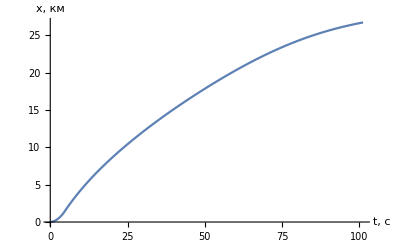

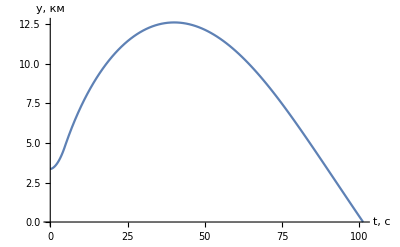

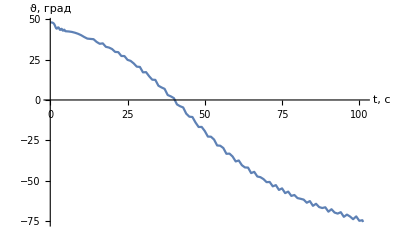

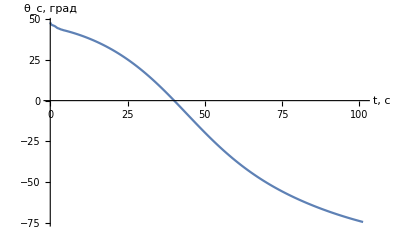

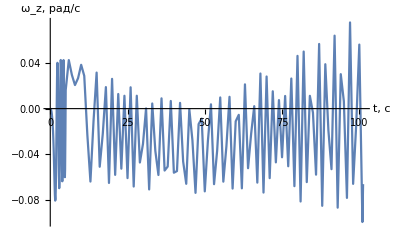

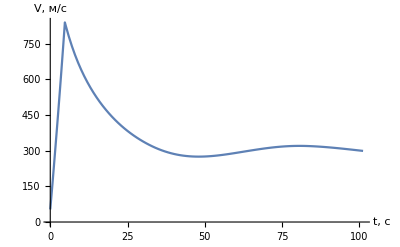

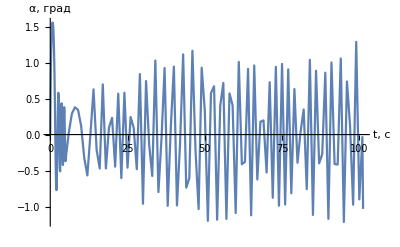

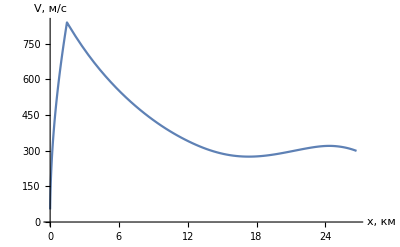

```mathematica
trash=0;(*сколько последних строчек таблицы выбросить*)
ListLinePlot[Table[{RezTab[[k+2,2]],RezTab[[k+2,16]]/1000},{k,n-trash}],AxesLabel->{"t, c","x, км"}]
ListLinePlot[Table[{RezTab[[k+2,2]],RezTab[[k+2,14]]/1000},{k,n-trash}],AxesLabel->{"t, c","y, км"}]
ListLinePlot[Table[{RezTab[[k+2,2]],RezTab[[k+2,13]]},{k,n-trash}],AxesLabel->{"t, c","ϑ, град"}]
ListLinePlot[Table[{RezTab[[k+2,2]],RezTab[[k+2,9]]},{k,n-trash}],AxesLabel->{"t, c","θ_(:0441), град"}]
ListLinePlot[Table[{RezTab[[k+2,2]],RezTab[[k+2,12]]},{k,n-trash}],AxesLabel->{"t, c","ω_z, рад/c"}]
ListLinePlot[Table[{RezTab[[k+2,2]],RezTab[[k+2,5]]},{k,n-trash}],AxesLabel->{"t, c","V, м/c"}]
ListLinePlot[Table[{RezTab[[k+2,2]],RezTab[[k+2,8]]},{k,n-trash}],AxesLabel->{"t, c","α, град"}]
ListLinePlot[Table[{RezTab[[k+2,16]]/1000,RezTab[[k+2,5]]},{k,n-trash}],AxesLabel->{"x, км","V, м/c"}]
ListLinePlot[Table[{RezTab[[k+2,16]]/1000,RezTab[[k+2,9]]},{k,n-trash}],AxesLabel->{"x, км","θ_(:0441), град"}]
ListLinePlot[Table[{RezTab[[k+2,16]]/1000,RezTab[[k+2,14]]/1000},{k,n-trash}],AxesLabel->{"x, км","y, км"}]
```

```mathematica
Export["C:\\Users\\Квай мембер Мрак\\Desktop\\ballu.xlsx",Table[RezTab[[k]],{k,n-trash}]]
```

C:\Users\Квай мембер Мрак\Desktop\ballu.xlsx